```mathematica
X = PauliMatrix[1];
Z = PauliMatrix[3];
Id = PauliMatrix[0];
Had = 1/Sqrt[2] {{1,1},{1,-1}};
ket0 = {{1},{0}};
ket1 = {{0},{1}};
(*4 qubit VQLS*)
(*A = 1/ζ(∑_(j=1)^n Subscript[X, j]+J∑_(j=1)^(n-1) Subscript[Z, j] Subscript[Z, j+1]+ηI)
b=H^(⊗n)|0>
*)
κ = 20;
```

```mathematica
A[ζ_, η_, J_] := 1/ζ (KroneckerProduct[X, KroneckerProduct[Id, KroneckerProduct[Id, Id]]]+KroneckerProduct[Id, KroneckerProduct[X, KroneckerProduct[Id, Id]]]+KroneckerProduct[Id, KroneckerProduct[Id, KroneckerProduct[X, Id]]]+KroneckerProduct[Id, KroneckerProduct[Id, KroneckerProduct[Id, X]]]+
J *(
KroneckerProduct[Z, KroneckerProduct[Z, KroneckerProduct[Id, Id]]]+KroneckerProduct[Id, KroneckerProduct[Z, KroneckerProduct[Z, Id]]]+
KroneckerProduct[Id, KroneckerProduct[Id, KroneckerProduct[Z, Z]]]
)+η IdentityMatrix[2^4]);
```

```mathematica
b = KroneckerProduct[Had, Had, Had, Had].KroneckerProduct[ket0, ket0, ket0, ket0]
```

{{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4}}

```mathematica
x = Inverse[A[10,10, 0.1] ].b
```

{{0.173379},{0.176765},{0.180336},{0.176812},{0.180336},{0.184103},{0.180384},{0.176765},{0.176765},{0.180384},{0.184103},{0.180336},{0.176812},{0.180336},{0.176765},{0.173379}}

```mathematica
x/Norm[x]
```

{{0.242642},{0.24738},{0.252378},{0.247446},{0.252378},{0.25765},{0.252445},{0.24738},{0.24738},{0.252445},{0.25765},{0.252378},{0.247446},{0.252378},{0.24738},{0.242642}}

```mathematica
(x/Norm[x])^2
```

{{0.0588749},{0.061197},{0.0636946},{0.0612297},{0.0636946},{0.0663837},{0.0637286},{0.061197},{0.061197},{0.0637286},{0.0663837},{0.0636946},{0.0612297},{0.0636946},{0.061197},{0.0588749}}

```mathematica
SingularValueList[A[10,10, 0.1]]
```

{1.40075,1.21671,1.20638,1.19404,1.18437,1.02234,1.01,1.00034,0.999665,0.99,0.977657,0.815629,0.805964,0.793621,0.783286,0.59925}

```mathematica
Exp[-20*t] == 0.9
```

ⅇ^(-20 t)==0.9

```mathematica
Solve[ⅇ^(-20 t)==0.9,{t},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→0.00526803}}

```mathematica
Solve[ⅇ^(-10 t)==0.9,{t},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→0.0105361}}

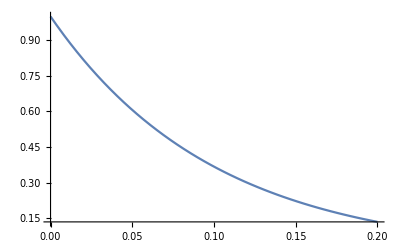

```mathematica
Plot[Exp[-10*Abs[t]], {t, 0,0.2}]
```

```mathematica
Exp[-10 0.013509063308791]
```

0.873637